```mathematica
a=Binarize[Import["/home/jirka/2.png"]];
{x,y}=ImageDimensions[a];
bod[{xc_,yc_}]:=ImageData[a][[Round[-yc-y/2],Round[xc-x/2]]]==0
```

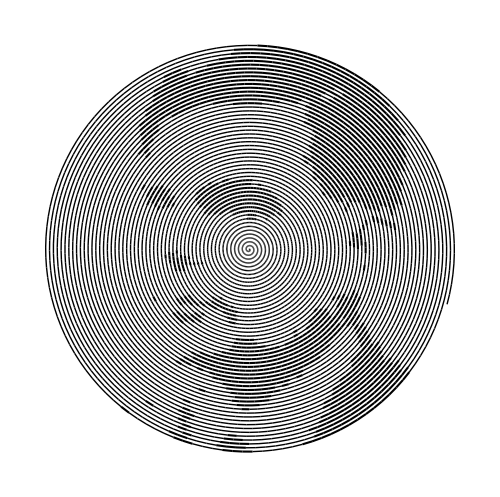

```mathematica
scale=2.5;
Table[{u*Sin[u], u*Cos[u]},{u,0,0.95scale*Min[x,y]/2,0.05}];
Partition[%,2,1];
If[bod[#[[1]]/scale],Unevaluated[Sequence[Thickness[0.003],Line[#]]],Unevaluated[Sequence[Thickness[0.002],Line[#]]]]&/@%;
Graphics[%,ImageSize->500]
```

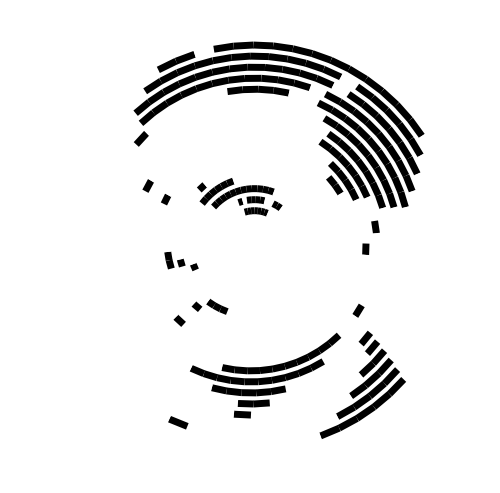

```mathematica
b=Import["/home/jirka/Desktop/Screenshot.png"];
b=ColorConvert[%,"Grayscale"];
{x2,y2}=ImageDimensions[b];
bod[{xc_,yc_}]:=(ImageData[b][[Round[-yc-y2/2],Round[xc-x2/2]]]-0.1)^(1/3)//Round;
bod[_]:=0.
scale=2;
Table[{u*Sin[u], u*Cos[u]},{u,0,0.95scale*Min[x2,y2]/2,0.1}];
Partition[%,2,1];
List[GrayLevel[bod[#[[1]]/scale]],Line[#] ]&/@%;
Graphics[{Thickness[0.01]}~Join~%//Flatten,ImageSize->500]
```

```mathematica
b=Import["/home/jirka/PMA/im/3.png"];
c=MorphologicalComponents[Binarize[b]];
c=DeleteSmallComponents[c,10];
pnts[{p_,count_}]:=RandomSample[Position[c,p],(count//N)^(1./1.5)//Ceiling];
ComponentMeasurements[c,"Count"]/.Rule[q_,w_]->{q,w};
pnts/@%;
Rotate[Graphics[((BSplineCurve[Sort[#,Norm[#1]<Norm[#2]&]~Append~#[[1]]])&/@Partition[#,10])&/@%],-90Degree]
```

-Graphics-